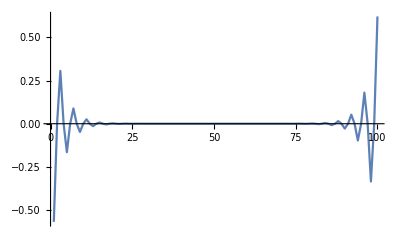

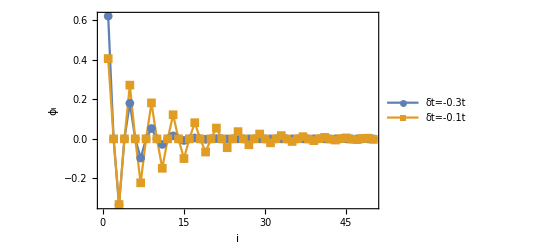

```mathematica
t=1;
t1=-0.3;
num=100;
matH=Table[KroneckerDelta[i,j+1](t+(-1)^i t1)+KroneckerDelta[i+1,j](t+(-1)^j t1),{i,1,num},{j,1,num}];
ev1=Eigenvectors[matH][[num-1]];
ev2=Eigenvectors[matH][[num]];
Clear[t1];
t1=-0.1;
matH=Table[KroneckerDelta[i,j+1](t+(-1)^i t1)+KroneckerDelta[i+1,j](t+(-1)^j t1),{i,1,num},{j,1,num}];
ev11=Eigenvectors[matH][[num-1]];
ev12=Eigenvectors[matH][[num]];
ListPlot[ev1,PlotRange->All,Joined->True]
f1=Table[ev2[[i]],{i,1,50}];
f2=Table[ev12[[i]],{i,1,50}];
SSHFunc=ListPlot[{f1,f2},PlotLegends->Placed[{"δt=-0.3t","δt=-0.1t"},{0.7,0.8}],PlotStyle->PointSize[Large],PlotRange->All,Joined->True,PlotMarkers->Automatic,Frame->True,FrameTicks->True,FrameStyle->Directive[Black,15,Thin,FontFamily->"Times New Roman"],FrameTicksStyle->Directive[Black,12,FontFamily->"Times New Roman"],FrameLabel->{i,Subscript[ϕ, i]}]
```

```mathematica
Export["C:\Users\Fluen\Desktop\李成蹊所有的note\shen-note\SSHFunc.pdf",SSHFunc]
```

C:\Users\Fluen\Desktop\李成蹊所有的note\shen-note\SSHFunc.pdf